```mathematica
M=1
m=0.1
R=1
r=0.01
g=10
L1=M*R^2*(ψ'[t])^2/2+m/2*(2 R^2*(θ'[t])^2+R^2*(ψ'[t])^2+2*R^2*θ'[t]*ψ'[t]-2*R*r*θ'[t])+m*g*R*Cos[θ[t]]
D[(D[L1,θ'[t]]), t]-D[L1,θ[t]]
D[(D[L1,ψ'[t]]), t]-D[L1,ψ[t]]
```

1

0.1

1

0.01

10

1. Cos[θ[t]]+1/2 ψ'[t]^2+0.05 (-0.02 θ'[t]+2 θ'[t]^2+2 θ'[t] ψ'[t]+ψ'[t]^2)

1. Sin[θ[t]]+0.05 (4 θ''[t]+2 ψ''[t])

ψ''[t]+0.05 (2 θ''[t]+2 ψ''[t])

{1. Sin[θ[t]]+0.05 (4 θ''[t]+2 ψ''[t])==0,ψ''[t]+0.05 (2 θ''[t]+2 ψ''[t])==0}

{θ[0]==0.1,θ'[0]==0.,ψ[0]==0,ψ'[0]==0.1}

{{θ→InterpolatingFunction[…],ψ→InterpolatingFunction[…]}}

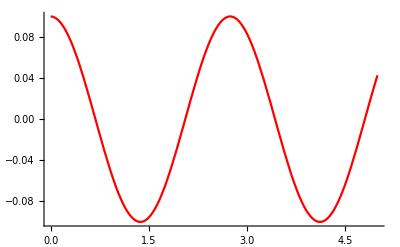

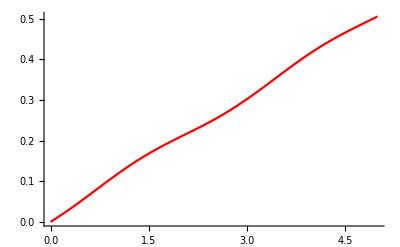

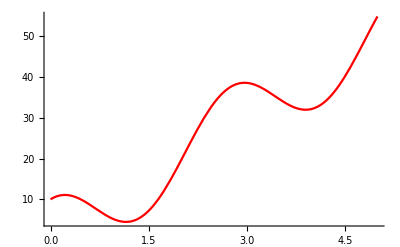

```mathematica
s1={D[(D[L1,θ'[t]]), t]-D[L1,θ[t]]==0,
D[(D[L1,ψ'[t]]), t]-D[L1,ψ[t]]==0}

ics={θ[0]== 0.10,θ'[0]== 0.0,ψ[0]==0,ψ'[0]==0.1}
sol1=NDSolve[{s1,ics},{θ,ψ},{t,0,200}]
Plot[Evaluate[θ[t]/.sol1],{t,0,5},PlotRange->All,PlotStyle->Red]
Plot[Evaluate[ψ[t]/.sol1],{t,0,5},PlotRange->All,PlotStyle->Red]
Plot[Evaluate[R*(ψ[t]+θ[t])/r/.sol1],{t,0,5},PlotRange->All,PlotStyle->Red]
```